```mathematica
pivot[iStar_, jStar_, tableau_] := (
newTableau = tableau;
numberRows = Dimensions[tableau][[1]];
numberCols = Dimensions[tableau][[2]];
(* switch row tableau variables *)
newTableau[[1,jStar]] = tableau[[iStar, numberCols]];
newTableau[[iStar, numberCols]] = tableau[[1,jStar]];
(* switch column tableau variables *)
newTableau[[numberRows,jStar]] = -tableau[[iStar, 1]];
newTableau[[iStar, 1]] = -tableau[[numberRows,jStar]];
(* adjust loop bounds to skip 1st column and last row *)
For[ii = 2, ii < numberRows, ii++,
For[jj=2,jj<numberCols,jj++,
If[ii == iStar && jj == jStar, 
newTableau[[ii,jj]]=1/tableau[[iStar, jStar]]];
If[ii== iStar && jj ≠ jStar,
newTableau[[ii,jj]]= -tableau[[iStar, jj]]/tableau[[iStar, jStar]]];
If[ii ≠ iStar && jj == jStar,
newTableau[[ii, jj]]= tableau[[ii, jStar]]/tableau[[iStar, jStar]]];
If[ii ≠ iStar && jj ≠ jStar,
newTableau[[ii,jj]] = tableau[[ii,jj]]-tableau[[iStar,jj]]*tableau[[ii, jStar]]/tableau[[iStar,jStar]]];
]
];
Return[newTableau];
)
```

3900

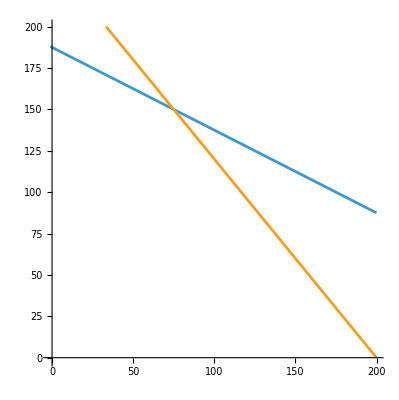

```mathematica
Clear[x1,x2]
z[x1_,x2_]:=24x1+28x2-3900
g1[x1_,x2_]:=4x1+8x2;
g2[x1_,x2_]:=6x1+5x2;
delz={24,28}; (* gradient of z *)
delg1={3,8};(* gradient of g1 *)
delg2={6,5};(* gradient of g2 *)
b1=1500;
b2=1200;
b3=0;
db1=0;
db2=0;
db3=0;
p1=1;
p2=2;
initialResourceCost=p1 b1+p2 b2
g1[x1_]:=x2/.Solve[g1[x1,x2]==b1,{x2}][[1,1]]
g2[x1_]:=x2/.Solve[g2[x1,x2]==b2,{x2}][[1,1]]
Plot[{g1[x],g2[x]},{x,-1,200},AspectRatio->Automatic,PlotRange->{-1,200},PlotHighlighting->None ]
```

```mathematica
m0={" ","y1","y2",1," "};
m1={"x1",4,6,-24,"v1"};
m2={"x2",8,5,-28,"v2"}; 
mobj={-1,b1+db1,b2+db2,-3900,"w→min"};
mLast={"",-"s1",-"s2","-z→min" ,""};
a={m0,m1,m2,mobj,mLast};
Print["db = ( ",db1," ",db2," ",db3," ) initial = ",MatrixForm[a]];
```

db = ( 0 0 0 ) initial = (  | y1 | y2 | 1 |  
x1 | 4 | 6 | -24 | v1
x2 | 8 | 5 | -28 | v2
-1 | 1500 | 1200 | -3900 | w→min
 | -s1 | -s2 | -z→min | )

```mathematica
b = pivot[2,2,a]
Print["db = ( ",db1," ",db2," ",db3," ) next step = ",MatrixForm[b]];
```

{{ ,v1,y2,1, },{s1,1/4,-3/2,6,y1},{x2,2,-7,20,v2},{-1,375,-1050,5100,w→min},{,-x1,-s2,-z→min,}}

db = ( 0 0 0 ) next step = (  | v1 | y2 | 1 |  
s1 | 1/4 | -3/2 | 6 | y1
x2 | 2 | -7 | 20 | v2
-1 | 375 | -1050 | 5100 | w→min
 | -x1 | -s2 | -z→min | )

```mathematica
c = pivot[3,3,b]
Print["db = ( ",db1," ",db2," ",db3," ) next step = ",MatrixForm[c]];
```

{{ ,v1,v2,1, },{s1,-5/28,3/14,12/7,y1},{s2,2/7,-1/7,20/7,y2},{-1,75,150,2100,w→min},{,-x1,-x2,-z→min,}}

db = ( 0 0 0 ) next step = (  | v1 | v2 | 1 |  
s1 | -5/28 | 3/14 | 12/7 | y1
s2 | 2/7 | -1/7 | 20/7 | y2
-1 | 75 | 150 | 2100 | w→min
 | -x1 | -x2 | -z→min | )

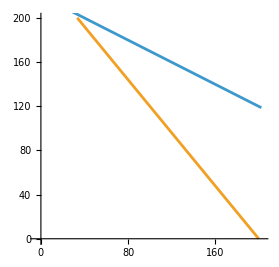
```mathematica
(*We should make 75 forms and 150 spoons. Profit is 2100. Revenue is 2100+3900 = 6000. We can get revenue by just adding back in that initial cost for resources(total money made before costs).*)

(*If no more ebony is available but pewter is available at $1.0/oz, should Joe bob buy more? If so, how much? If not, should he sell? How much?*)

(*Here we use the dual solution to find the answer to this problem. p1 = $1 < y1 = 12/7, so we should buy more pewter. To calculate how much he should buy we need to calculate db1 max to see how much we can push up the pewter constraint until the dual solution changes.*)
-Graphics-
```

```mathematica
(*We can push up constraint one until the intersection of the x2 axis and g2.*)
Solve[g2[u,v] ==  b2 && u ==0]
```

{{u→0,v→240}}

```mathematica
b1Max = g1[0,240]
db1Max = b1Max - b1
```

1920

420

```mathematica
(*We should buy 420 ounces of pewter. *)
```

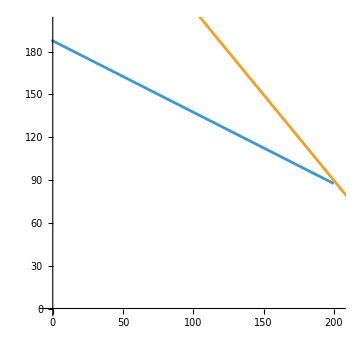
```mathematica
(*If no more pewter is available but ebony is available at $2.0 an ounce, should Joe Bob buy more? If so, how much more? If not, should he sell? How much?*)
(*Here we look at if p2 < y2. p2 = 2 < y2 = 20/7, so yes we should buy. If it was less than we should sell and calculate db2 min, but it's not so we look for db2Max.*)
-Graphics-
```

```mathematica
(*Whenever g1 intersects with the x-axis is when we constraint 2 becomes inactive and the dual solution changes. So we can solve for that point as the maximum amount of ebony to buy in excess.*)
Solve[g1[u,v]==b1 && v==0]
```

{{u→375,v→0}}

```mathematica
b2Max = g2[375,0]
db2Max = b2Max - b2
```

2250

1050

```mathematica
(*We should buy 1050 ounces in excess of ebony*)
(*D: If both pewter and ebony are available, at 1/oz, and 2/oz, respectively, how much of each should Joe Bob buy if he only has 1000 to spend. *)
(*This essentially says we add two more variables, x3 & x4, to represent a new potential stream of revenue, and a new constraint to represent our capital expendature constraints.*)
```

```mathematica
(* Modify LP for d: include x3=db1 and x4=db2
max z= 24x1+28x2-3900
4x1+8x2-1x3+0x4<=1500
6x1+5x2+0x3-1x4<=1200
0x1+0x2+1x3+2x4<=1000
x>=0 *)
a0 = {"", "y1", "y2", "y3", 1, ""};
a1 = {"x1", 4, 6, 0, -24, "v1"};
a2 = {"x2", 8, 5, 0,-28, "v2"};
a3 = {"x3", -1, 0, 1,1, "v3"};
a4 = {"x4", 0, -1, 2,2, "v4"};
aObj = {-1, 1500., 1200., 1000., -3900., "w->min"};
aLast = {"", -"s1", -"s2", -"s3", -"z->min", ""};
a={a0,a1,a2,a3,a4,aObj,aLast};
Print["a = ",MatrixForm[a] ]
```

a = ( | y1 | y2 | y3 | 1 | 
x1 | 4 | 6 | 0 | -24 | v1
x2 | 8 | 5 | 0 | -28 | v2
x3 | -1 | 0 | 1 | 1 | v3
x4 | 0 | -1 | 2 | 2 | v4
-1 | 1500. | 1200. | 1000. | -3900. | w->min
 | -s1 | -s2 | -s3 | -z->min | )

```mathematica
|
```

a = ( | y1 | y2 | y3 | 1 | 
x1 | 4 | 6 | 0 | -24 | v1
x2 | 8 | 5 | 0 | -28 | v2
x3 | -1 | 0 | 1 | 1 | v3
x4 | 0 | -1 | 2 | 2 | v4
-1 | 1500. | 1200. | 1000. | -3900. | w->min
 | -s1 | -s2 | -s3 | -z->min | )

```mathematica
b=pivot[2,2,a];
Print["b = ",MatrixForm[b] ]
```

b = ( | v1 | y2 | y3 | 1 | 
s1 | 1/4 | -3/2 | 0 | 6 | y1
x2 | 2 | -7 | 0 | 20 | v2
x3 | -1/4 | 3/2 | 1 | -5 | v3
x4 | 0 | -1 | 2 | 2 | v4
-1 | 375. | -1050. | 1000. | 5100. | w->min
 | -x1 | -s2 | -s3 | -z->min | )

```mathematica
c=pivot[3,3,b];
Print["c = ",MatrixForm[c] ]
```

c = ( | v1 | v2 | y3 | 1 | 
s1 | -5/28 | 3/14 | 0 | 12/7 | y1
s2 | 2/7 | -1/7 | 0 | 20/7 | y2
x3 | 5/28 | -3/14 | 1 | -5/7 | v3
x4 | -2/7 | 1/7 | 2 | -6/7 | v4
-1 | 75. | 150. | 1000. | 2100. | w->min
 | -x1 | -x2 | -s3 | -z->min | )

```mathematica
d=pivot[4,4,c];
Print["d = ",MatrixForm[d] ]
```

d = ( | v1 | v2 | v3 | 1 | 
s1 | -5/28 | 3/14 | 0 | 12/7 | y1
s2 | 2/7 | -1/7 | 0 | 20/7 | y2
s3 | -5/28 | 3/14 | 1 | 5/7 | y3
x4 | -9/14 | 4/7 | 2 | 4/7 | v4
-1 | -103.571 | 364.286 | 1000. | 2814.29 | w->min
 | -x1 | -x2 | -x3 | -z->min | )

```mathematica
e=pivot[5,2,d];
Print["e = ",MatrixForm[e] ]
```

e = ( | v4 | v2 | v3 | 1 | 
s1 | 5/18 | 1/18 | -5/9 | 14/9 | y1
s2 | -4/9 | 1/9 | 8/9 | 28/9 | y2
s3 | 5/18 | 1/18 | 4/9 | 5/9 | y3
x1 | -14/9 | 8/9 | 28/9 | 8/9 | v1
-1 | 161.111 | 272.222 | 677.778 | 2722.22 | w->min
 | -x4 | -x2 | -x3 | -z->min | )

```mathematica
(*Here we interpret the anser by pulling the basic solution directly out of the tableaux. We should make 272.22 forks, buy 677.78 oz of pewter, and 161.11 oz of ebony. We should expect a profit of 2722.22 dollars.*)
```

10500

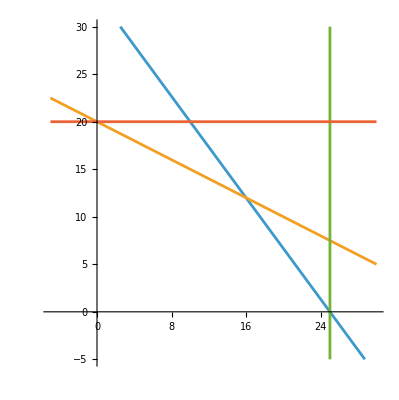

```mathematica
(*12.2*)
Clear[x1,x2]
z[x1_,x2_]:=500x1+750x2-5100
g1[x1_,x2_]:=20x1+15x2;b1=500;
g2[x1_,x2_]:=10x1+20x2;b2=400;
g3[x1_,x2_]:=1x1+0x2;b3=25;
g3grph[x1_,x2_]:=1*10^6x1+1x2;b3grph=25*10^6;
g4[x1_,x2_]:=0x1+1x2;b4=20;
delz={500,750}; (* gradient of z *)
delg1={10,20};(* gradient of g1 *)
delg2={20,15};(* gradient of g2 *)
p1=9;
p2=22.5;
initialResourceCost=4500+6000
g1[x1_]=x2/.Solve[g1[x1,x2]==b1][[1,1]];
g2[x1_]=x2/.Solve[g2[x1,x2]==b2][[1,1]];
g3[x1_]=x2/.Solve[g3grph[x1,x2]==b3grph][[1,1]];
g4[x1_]=x2/.Solve[g4[x1,x2]==b4][[1,1]];Plot[{g1[x],g2[x],g3[x],g4[x]},{x,-5,30},AspectRatio->Automatic,PlotHighlighting->None,PlotRange->{-5,30}]
```

```mathematica
a0 = {"", "y1", "y2","y3","y4", 1, ""};
a1 = {"x1", 20, 10,1 ,0,-500, "v1"};
a2 = {"x2", 15, 20,0,1,-750, "v2"};
aObj = {-1, 500, 400,25,20, -10500, "w->min"};
aLast = {"", -"s1", -"s2", -"s3",-"s4",-"z->min", ""};
a={a0,a1,a2,aObj,aLast};
Print["a = ",MatrixForm[a] ]
```

a = ( | y1 | y2 | y3 | y4 | 1 | 
x1 | 20 | 10 | 1 | 0 | -500 | v1
x2 | 15 | 20 | 0 | 1 | -750 | v2
-1 | 500 | 400 | 25 | 20 | -10500 | w->min
 | -s1 | -s2 | -s3 | -s4 | -z->min | )

```mathematica
(*a: What mix of A & B valves maxmizes profit w/o using ot and extra mats?*)
b = pivot[2,2,a]
Print["b = ",MatrixForm[b] ]
```

{{,v1,y2,y3,y4,1,},{s1,1/20,-1/2,-1/20,0,25,y1},{x2,3/4,25/2,-3/4,1,-375,v2},{-1,25,150,0,20,2000,w->min},{,-x1,-s2,-s3,-s4,-z->min,}}

b = ( | v1 | y2 | y3 | y4 | 1 | 
s1 | 1/20 | -1/2 | -1/20 | 0 | 25 | y1
x2 | 3/4 | 25/2 | -3/4 | 1 | -375 | v2
-1 | 25 | 150 | 0 | 20 | 2000 | w->min
 | -x1 | -s2 | -s3 | -s4 | -z->min | )

```mathematica
c=pivot[3,3,b]
Print["c =", MatrixForm[c]]
```

{{,v1,v2,y3,y4,1,},{s1,2/25,-1/25,-2/25,1/25,10,y1},{s2,-3/50,2/25,3/50,-2/25,30,y2},{-1,16,12,9,8,6500,w->min},{,-x1,-x2,-s3,-s4,-z->min,}}

c =( | v1 | v2 | y3 | y4 | 1 | 
s1 | 2/25 | -1/25 | -2/25 | 1/25 | 10 | y1
s2 | -3/50 | 2/25 | 3/50 | -2/25 | 30 | y2
-1 | 16 | 12 | 9 | 8 | 6500 | w->min
 | -x1 | -x2 | -s3 | -s4 | -z->min | )

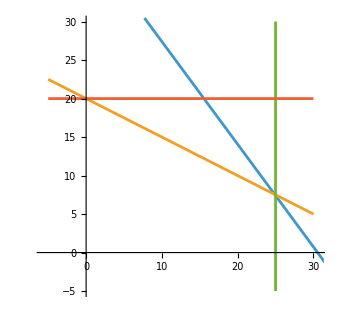
```mathematica
(*Make 16 type a valves and 12 type b values.*)
(*part b: should we have any extra material without scheduling ot? Yes, y1 = 10 > p1 = $9/lb*)
-Graphics-
```

```mathematica
(*We can increase material until we hit the demand constraint of the type a valve*)
Solve[g2[u,v]==b2 && u==25]
```

{{u→25,v→15/2}}

```mathematica
b1Max = g1[25,15/2]
db1Max = b1Max - b1
```

1225/2

225/2

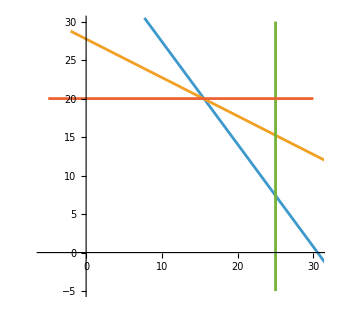
```mathematica
(*we should buy 225/2 lbs of extra material. *)
(*c: Should the company schedule overtime assuming it has already taken whatever action was determined to be optimal in b? If so, how much? *)
(*yes, the dual solution doesn't change when we make this adjustment and y2 = 30 > 22.50 = p2.*)
-Graphics-
```

```mathematica
Solve[g1[u,v]==b1Max && v==20]
```

{{u→125/8,v→20}}

```mathematica
b2Max = g2[125/8,20] 
db2Max = b2Max - b2
```

2225/4

625/4

```mathematica
db1 = 225/2
db2 = 625/4
a0 = {"", "y1", "y2","y3","y4", 1, ""};
a1 = {"x1", 20, 10,1 ,0,-500, "v1"};
a2 = {"x2", 15, 20,0,1,-750, "v2"};
aObj = {-1, 500+db1, 400+db2,25,20, -(10500-(9*225/2)), "w->min"};
aLast = {"", -"s1", -"s2", -"s3",-"s4",-"z->min", ""};
a={a0,a1,a2,aObj,aLast};
Print["new a with db1 and db2 = ", MatrixForm[a]]
```

225/2

625/4

new a with db1 and db2 = ( | y1 | y2 | y3 | y4 | 1 | 
x1 | 20 | 10 | 1 | 0 | -500 | v1
x2 | 15 | 20 | 0 | 1 | -750 | v2
-1 | 1225/2 | 2225/4 | 25 | 20 | -17625/2 | w->min
 | -s1 | -s2 | -s3 | -s4 | -z->min | )

```mathematica
b = pivot[2,2,a]
c=pivot[3,3,b]
Print["optimal c = ", MatrixForm[c]]
```

{{,v1,y2,y3,y4,1,},{s1,1/20,-1/2,-1/20,0,25,y1},{x2,3/4,25/2,-3/4,1,-375,v2},{-1,245/8,250,-45/8,20,6500,w->min},{,-x1,-s2,-s3,-s4,-z->min,}}

{{,v1,v2,y3,y4,1,},{s1,2/25,-1/25,-2/25,1/25,10,y1},{s2,-3/50,2/25,3/50,-2/25,30,y2},{-1,125/8,20,75/8,0,14000,w->min},{,-x1,-x2,-s3,-s4,-z->min,}}

optimal c = ( | v1 | v2 | y3 | y4 | 1 | 
s1 | 2/25 | -1/25 | -2/25 | 1/25 | 10 | y1
s2 | -3/50 | 2/25 | 3/50 | -2/25 | 30 | y2
-1 | 125/8 | 20 | 75/8 | 0 | 14000 | w->min
 | -x1 | -x2 | -s3 | -s4 | -z->min | )

```mathematica
(*get a level set,*)
d = pivot[3,5,c]
Print["Other side of the level set", MatrixForm[d]]
```

{{,v1,v2,y3,y2,1,},{s1,1/20,0,-1/20,-1/2,25,y1},{s4,-3/4,1,3/4,-25/2,375,y4},{-1,125/8,20,75/8,0,14000,w->min},{,-x1,-x2,-s3,-s2,-z->min,}}

Other side of the level set( | v1 | v2 | y3 | y2 | 1 | 
s1 | 1/20 | 0 | -1/20 | -1/2 | 25 | y1
s4 | -3/4 | 1 | 3/4 | -25/2 | 375 | y4
-1 | 125/8 | 20 | 75/8 | 0 | 14000 | w->min
 | -x1 | -x2 | -s3 | -s2 | -z->min | )

```mathematica
(*We should hire 625/4 more hours worth of labor. *)
```

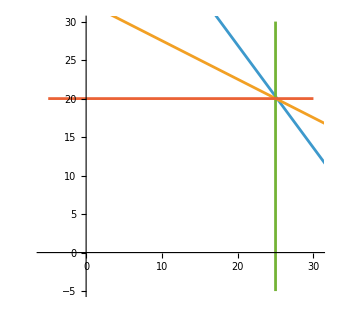
```mathematica
(*Part d: Assume the company always gets paid for the product it produces each week after it must pay for any extra material and labor it uses in that week, and before it must pay for any extra material and labor it uses in the following week, how much extra investment captial does the company need to maxmize profit?*)
(*This is basically asking how much should we increase the amt we can spend on labor and materials until we hit the demand constraint.*)
-Graphics-
```

```mathematica
(*Material lbs needed for 25 A & 20 B *) 
b1d=g1[25,20]
(*Labor hrs needed for 25 A & 20 B*)
b2d=g2[25,20]
(*Extra lbs material needed for 25 A & 20 B *)
db1d=b1d-b1
(* Extra labor hrs needed for 25 A & 20 B *) 
db2d=b2d-b2
(* Cost of extra material needed for 25 A & 20 B *)
db1dCost=p1 db1d
(* Cost of extra labor needed for 25 A & 20 B *)
db2dCost=p2 db2d
(* Answer to d is total investment needed = cost of extra material + cost of extra labor. 
Budget is constraint b5 so extra investment is db5. *)
totalInvestmentd=db1dCost+db2dCost
```

800

650

300

250

2700

5625.

8325.

```mathematica
(*Part e: If the company only has $5000 available investment captial to increase production, what allocation of those funds for more material and labor maximizes firm's net profit?*)
(*This is just saying we should need to add an investment captial constraint, so we can't just maximize production to the demand limits and solve.*)

roiMats = (10 - p1)/p1
roiLabor = (30-p2)/p2
(*Labor makes us more money with limited capital, so we should make out labor first.*)
```

1/9

0.333333

```mathematica
Solve[g1[u,v]==b1 && g4[u,v] ==b4]
```

{{u→10,v→20}}

```mathematica
g2[10,20](*in the original solved LP, we can only spend up to 2250 without buying more mats, so we should alter the amount of mats we are buying for a new lp.*)
```

500

```mathematica
100*22.50
```

2250.

```mathematica
z[x1_,x2_,x3_,x4_]:=500x1+750x2+-9x3-22.50x4-10500;
g1[x1_,x2_,x3_,x4_]:= 20x1+15x2-x3-0x4; 
g2[x1_,x2_,x3_,x4_]:=10x1+20x2+0x3-x4;
g3[x1_,x2_,x3_,x4_]:=x1+0x2+0x3+0x4; 
g4[x1_,x2_,x3_,x4_]:=0x1+x2+0x3+0x4;
g5[x1_,x2_,x3_,x4_] :=0x1+0x2+9x3+22.50x4; 
b5=5000; 
b4=20;
b3=25;
```

```mathematica
a0 = {"", "y1", "y2", "y3","y4","y5",1,""};
a1 = {"x1", 20, 10,1,0, 0, -500, "v1"};
a2 = {"x2", 15, 20,0,1, 0,-750, "v2"};
a3 = {"x3", -1, 0,0, 0,9,9, "v3"};
a4 = {"x4", 0, -1,0, 0,45/2,45/2, "v4"};
aObj = {-1, 500., 400.,25,20, 5000., -10500., "w->min"};
aLast = {"", -"s1", -"s2", -"s3",-"s4",-"s5", -"z->min", ""};
a={a0,a1,a2,a3,a4,aObj,aLast};
Print["a = ",MatrixForm[a] ]
```

a = ( | y1 | y2 | y3 | y4 | y5 | 1 | 
x1 | 20 | 10 | 1 | 0 | 0 | -500 | v1
x2 | 15 | 20 | 0 | 1 | 0 | -750 | v2
x3 | -1 | 0 | 0 | 0 | 9 | 9 | v3
x4 | 0 | -1 | 0 | 0 | 45/2 | 45/2 | v4
-1 | 500. | 400. | 25 | 20 | 5000. | -10500. | w->min
 | -s1 | -s2 | -s3 | -s4 | -s5 | -z->min | )

```mathematica
b=pivot[2,2,a];
Print["b = ",MatrixForm[b] ]
```

b = ( | v1 | y2 | y3 | y4 | y5 | 1 | 
s1 | 1/20 | -1/2 | -1/20 | 0 | 0 | 25 | y1
x2 | 3/4 | 25/2 | -3/4 | 1 | 0 | -375 | v2
x3 | -1/20 | 1/2 | 1/20 | 0 | 9 | -16 | v3
x4 | 0 | -1 | 0 | 0 | 45/2 | 45/2 | v4
-1 | 25. | 150. | 0. | 20. | 5000. | 2000. | w->min
 | -x1 | -s2 | -s3 | -s4 | -s5 | -z->min | )

```mathematica
c=pivot[2,3,b];
Print["c = ",MatrixForm[c] ]
```

c = ( | v1 | y1 | y3 | y4 | y5 | 1 | 
s2 | 1/10 | -2 | -1/10 | 0 | 0 | 50 | y2
x2 | 2 | -25 | -2 | 1 | 0 | 250 | v2
x3 | 0 | -1 | 0 | 0 | 9 | 9 | v3
x4 | -1/10 | 2 | 1/10 | 0 | 45/2 | -55/2 | v4
-1 | 40. | -300. | -15. | 20. | 5000. | 9500. | w->min
 | -x1 | -s1 | -s3 | -s4 | -s5 | -z->min | )

```mathematica
d=pivot[4,3,c];
Print["d = ",MatrixForm[d] ]
```

d = ( | v1 | v3 | y3 | y4 | y5 | 1 | 
s2 | 1/10 | 2 | -1/10 | 0 | -18 | 32 | y2
x2 | 2 | 25 | -2 | 1 | -225 | 25 | v2
s1 | 0 | -1 | 0 | 0 | 9 | 9 | y1
x4 | -1/10 | -2 | 1/10 | 0 | 81/2 | -19/2 | v4
-1 | 40. | 300. | -15. | 20. | 2300. | 6800. | w->min
 | -x1 | -x3 | -s3 | -s4 | -s5 | -z->min | )

```mathematica
e=pivot[3,4,d];
Print["e = ",MatrixForm[e] ]
```

e = ( | v1 | v3 | v2 | y4 | y5 | 1 | 
s2 | 0 | 3/4 | 1/20 | -1/20 | -27/4 | 123/4 | y2
s3 | 1 | 25/2 | -1/2 | 1/2 | -225/2 | 25/2 | y3
s1 | 0 | -1 | 0 | 0 | 9 | 9 | y1
x4 | 0 | -3/4 | -1/20 | 1/20 | 117/4 | -33/4 | v4
-1 | 25. | 112.5 | 7.5 | 12.5 | 3987.5 | 6612.5 | w->min
 | -x1 | -x3 | -x2 | -s4 | -s5 | -z->min | )

```mathematica
f=pivot[2,5,e];
Print["f = ",MatrixForm[f] ]
```

f = ( | v1 | v3 | v2 | y2 | y5 | 1 | 
s4 | 0 | 15 | 1 | -20 | -135 | 615 | y4
s3 | 1 | 20 | 0 | -10 | -180 | 320 | y3
s1 | 0 | -1 | 0 | 0 | 9 | 9 | y1
x4 | 0 | 0 | 0 | -1 | 45/2 | 45/2 | v4
-1 | 25. | 300. | 20. | -250. | 2300. | 14300. | w->min
 | -x1 | -x3 | -x2 | -s2 | -s5 | -z->min | )

```mathematica
g=pivot[5,5,f];
Print["g = ",MatrixForm[g] ]
```

g = ( | v1 | v3 | v2 | v4 | y5 | 1 | 
s4 | 0 | 15 | 1 | 20 | -585 | 165 | y4
s3 | 1 | 20 | 0 | 10 | -405 | 95 | y3
s1 | 0 | -1 | 0 | 0 | 9 | 9 | y1
s2 | 0 | 0 | 0 | -1 | 45/2 | 45/2 | y2
-1 | 25. | 300. | 20. | 250. | -3325. | 8675. | w->min
 | -x1 | -x3 | -x2 | -x4 | -s5 | -z->min | )

```mathematica
h=pivot[3,6,g];
Print["h = ",MatrixForm[h] ]
```

h = ( | v1 | v3 | v2 | v4 | y3 | 1 | 
s4 | -13/9 | -125/9 | 1 | 50/9 | 13/9 | 250/9 | y4
s5 | 1/405 | 4/81 | 0 | 2/81 | -1/405 | 19/81 | y5
s1 | 1/45 | -5/9 | 0 | 2/9 | -1/45 | 100/9 | y1
s2 | 1/18 | 10/9 | 0 | -4/9 | -1/18 | 250/9 | y2
-1 | 16.7901 | 135.802 | 20. | 167.901 | 8.20988 | 7895.06 | w->min
 | -x1 | -x3 | -x2 | -x4 | -s3 | -z->min | )

```mathematica
(*We should have 135.802 lbs of extra mats and and 167.901 extra hours of labor.*)
```

```mathematica
(*Before going into f, we should consider the similarities of having a level set. dzStar=(y1Star - p1)db1 *)
```